FittedModel[-0.0443595+6.16595×10^-7 x^2]

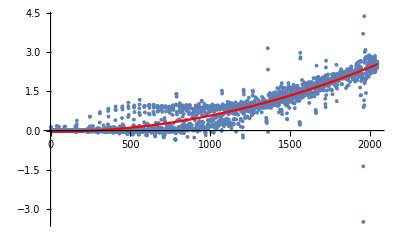

0.906359

{0.000221321,3.58333208272×10^-764}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "contains-fixed-i"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a +c*x^2,{a,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```